```mathematica
SetDirectory[NotebookDirectory[]];
Clear["Global`*"];
```

```mathematica
Decreasing of residue(n is number of nodes);
```

```mathematica
(*triangle 1*)
```

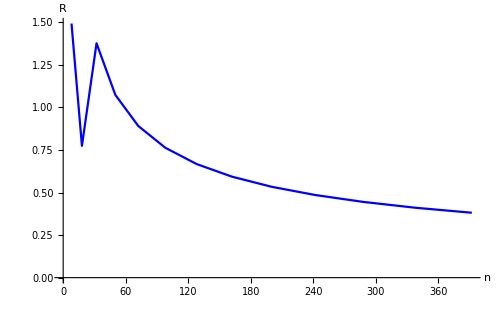

```mathematica
residueT1 = {{8,1.49288},{18,0.774385},{32,1.37695},{50,1.07424},{72,0.891276},{98,0.763024},{128,0.667378},{162,0.593141},{200,0.533801},{242,0.485267},{288,0.444828},{338,0.410613},{392,0.381286}};
gr1=ListLinePlot[residueT1,
GridLines->Full,
ImageSize->500,
PlotStyle->{Blue},
PlotRange->All,
AxesLabel->{Style["n",16,Black,Italic,FontFamily->"Times"],Style["R",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,Axes->True]
```

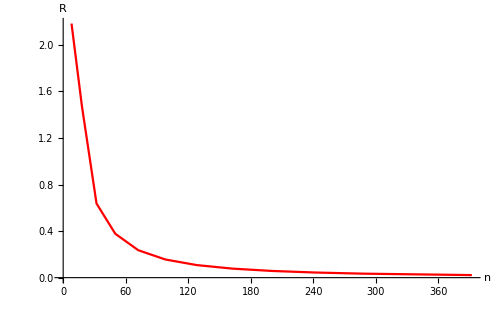

```mathematica
(*triangle 2*)
residueT2= {{8,2.18414},{18,1.4732},{32,0.636934},{50,0.377167},{72,0.235945},{98,0.156106},{128,0.108174},{162,0.0778432},{200,0.0577864},{242,0.0440251},{288, 0.0342846},{392,0.0219387}};
gr2=ListLinePlot[residueT2,
GridLines->Full,
ImageSize->500,
PlotStyle->{Red},
PlotRange->All,
AxesLabel->{Style["n",16,Black,Italic,FontFamily->"Times"],Style["R",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,Axes->True]
```

```mathematica
(*rectangle 1*)
```

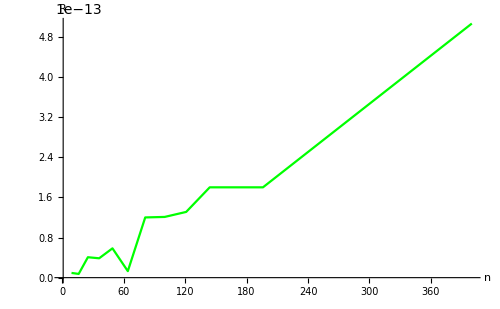

```mathematica
residueR1 = {{9,9.41*10^-15},{16, 7.45*10^-15},{25,4.07*10^-14},{36,3.86*10^-14},{49,5.84*10^-14},{64,1.3*10^-14},{81,1.2*10^-13},{100,1.21*10^-13},{121,1.31*10^-13},{144,1.8*10^-13},{169,1.8*10^-13},{196,1.8*10^-13},{400,5.06404*10^-13}};
gr3=ListLinePlot[residueR1,
GridLines->Full,
ImageSize->500,
PlotStyle->{Green},
PlotRange->All,
AxesLabel->{Style["n",16,Black,Italic,FontFamily->"Times"],Style["R",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,Axes->True]
```

```mathematica
(*rectangle 2*)
```

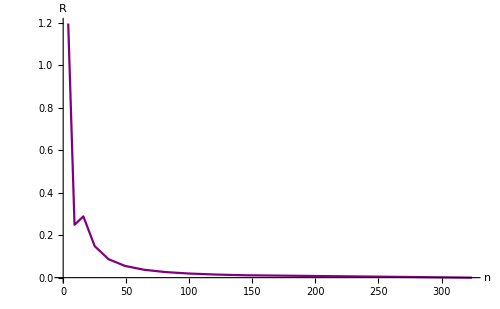

```mathematica
residueR2= {{4,1.19732},{9, 0.249047},{16,0.288585},{25,0.148413},{36,0.0868982},{49,0.0552596},{64,0.0373004},{81,0.0263593},{100,0.0193099},{121,0.0145698},{144,0.011259},{324,1.83755*10^-12}};
gr4=ListLinePlot[residueR2,
GridLines->Full,
ImageSize->500,
PlotStyle->{Purple},
PlotRange->All,
AxesLabel->{Style["n",16,Black,Italic,FontFamily->"Times"],Style["R",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,Axes->True]
```

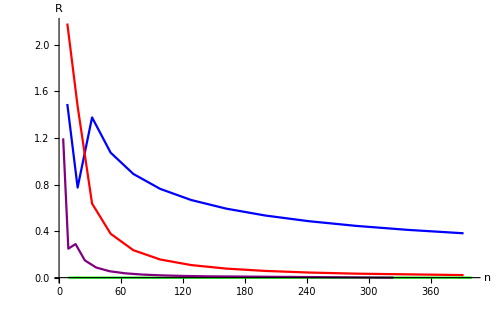

```mathematica
Show[gr1,gr2,gr3,gr4,PlotRange->All]
```

```mathematica
Decreasing of residue(n is number of finite elements);
```

```mathematica
nodes=40;
Print["Triangles 1"]
Table[{i,(i-1)(i-1)*2},{i,2,nodes}]
Print["Triangles 2"]
Table[{i,(i-1)/2(i-1)/2*2},{i,2,nodes}]
Print["Rectangles 1"]
Table[{i,(i-1)(i-1)},{i,2,nodes}]
Print["Rectangles 2"]
Table[{i,(i-1)/2(i-1)/2},{i,2,nodes}]
```

Triangles 1

{{2,2},{3,8},{4,18},{5,32},{6,50},{7,72},{8,98},{9,128},{10,162},{11,200},{12,242},{13,288},{14,338},{15,392},{16,450},{17,512},{18,578},{19,648},{20,722},{21,800},{22,882},{23,968},{24,1058},{25,1152},{26,1250},{27,1352},{28,1458},{29,1568},{30,1682},{31,1800},{32,1922},{33,2048},{34,2178},{35,2312},{36,2450},{37,2592},{38,2738},{39,2888},{40,3042}}

Triangles 2

{{2,1/2},{3,2},{4,9/2},{5,8},{6,25/2},{7,18},{8,49/2},{9,32},{10,81/2},{11,50},{12,121/2},{13,72},{14,169/2},{15,98},{16,225/2},{17,128},{18,289/2},{19,162},{20,361/2},{21,200},{22,441/2},{23,242},{24,529/2},{25,288},{26,625/2},{27,338},{28,729/2},{29,392},{30,841/2},{31,450},{32,961/2},{33,512},{34,1089/2},{35,578},{36,1225/2},{37,648},{38,1369/2},{39,722},{40,1521/2}}

Rectangles 1

{{2,1},{3,4},{4,9},{5,16},{6,25},{7,36},{8,49},{9,64},{10,81},{11,100},{12,121},{13,144},{14,169},{15,196},{16,225},{17,256},{18,289},{19,324},{20,361},{21,400},{22,441},{23,484},{24,529},{25,576},{26,625},{27,676},{28,729},{29,784},{30,841},{31,900},{32,961},{33,1024},{34,1089},{35,1156},{36,1225},{37,1296},{38,1369},{39,1444},{40,1521}}

Rectangles 2

{{2,1/4},{3,1},{4,9/4},{5,4},{6,25/4},{7,9},{8,49/4},{9,16},{10,81/4},{11,25},{12,121/4},{13,36},{14,169/4},{15,49},{16,225/4},{17,64},{18,289/4},{19,81},{20,361/4},{21,100},{22,441/4},{23,121},{24,529/4},{25,144},{26,625/4},{27,169},{28,729/4},{29,196},{30,841/4},{31,225},{32,961/4},{33,256},{34,1089/4},{35,289},{36,1225/4},{37,324},{38,1369/4},{39,361},{40,1521/4}}